# 21 Gaussian Elimination: Pivoting

## Solving a Linear System with an LU Decomposition

We know how to solve triangular systems. we even know that the obvious algorithm is backwards stable. We now know how to split a matrix up into two triangular matrices A=L.U.  we should be able to put this together to get an algorithm to solve A.x=L.U.x=b. All we need to do is make up an intermediate variable.  y=U.x 
	L.(U.x)=L.y=b
Solve L.y=b to get a ỹ.  Then solve U.x=ỹ to get x̃.  Since the triangular solves are backwards stable this would all be great if the L.U decomposition was stable!  It is not!

### Need for Pivoting

There are perfectly well behaved linear systems which will break our first attempt at an LU decomposition.  For example
	(ϵ | 1.0
1.0 | 1.0).(x1
x2)=(b1
b2).
In exact arithmetic Gaussian elimination gives the solution
	x1 | = | (b1-b2)/(-1+ϵ) | ⟶ | b2-b1
x2 | = | (-b1+b2 ϵ)/(-1+ϵ) | ⟶ | b1
The system is fine as ϵ→0.  Our first attempt at an LU decomposition gives. 
	A=(ϵ | 1.0
1.0 | 1.0)=(1 | 0
ϵ^-1 | 1)(ϵ | 1.0
0 | 1-ϵ^-1)
which in exact arithmetic works just fine: exact arithmetic does not care that ϵ^-1 could be huge. On any computer this is a real problem!  When ϵ is small in floating point the last entry gets messed up and we will get 
	 (1 | 0
ϵ^-1 | 1)(ϵ | 1.0
0 | -ϵ^-1)=(ϵ | 1
1 | 0)

The sad thing is this has nothing to do with the equations/matrix. As ϵ→0 the condition number κ(A) is the singular value ratio of ratio of (0 | 1.0
1.0 | 1.0) which is roughly 3.

The really sad thing is that if we had just written down the equations in a different order we would have got (1.0 | 1.0
ϵ | 1.0)=(1 | 0
ϵ | 1)(1 | 1
0 | 1-ϵ) which would have worked just fine.

We can not write a usage guide for a function that says “make sure your equations” are in a decent order. We need to make an algorithm that reorders the equations (rows in the matrix) into a good order on the fly.

The first question is given a matrix A which row (same as equation) should we start with.

After the first row we just ask which of the remaining rows is best to do next.

The resulting algorithm is called an LU decomposition with row pivoting.

You can also ask which remaining variable (column of the matrix would be best) which gives column pivoting.

If you ask which is the best variable and equation you are doing complete pivoting!

## LU Decomposition with row pivoting

Here is an unpivoted and uncommented LU Decomposition function

```mathematica
NoPivotLU[A_]:=Module[{m=Length[A],L,U=A},
L=IdentityMatrix[m];
Do[
Do[
L⟦j,k⟧=U⟦j,k⟧/U⟦k,k⟧;
U⟦j,k;;m⟧-=L⟦j,k⟧ U⟦k,k;;m⟧,
{j,k+1,m}],
{k,1,m-1}];
{L,U}
]
```

As always test.

```mathematica
m=34;
A=RandomReal[{-1,1},{m,m}];
{L,U}=NoPivotLU[A];
Norm[L.U-A]
```

8.51682×10^-14

We are going to convert it to a row pivoted code!

### Tracking Row Interchanges Plan

Software (Julia, Mathematica, etc.) return a list of the final order of the rows which they called p along with the entries in the

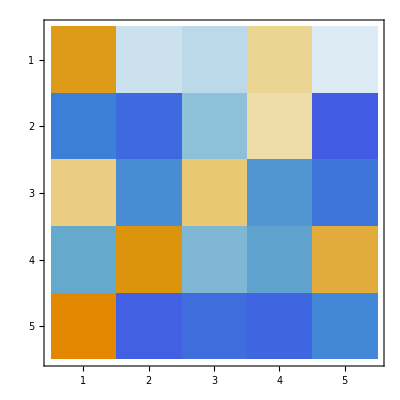
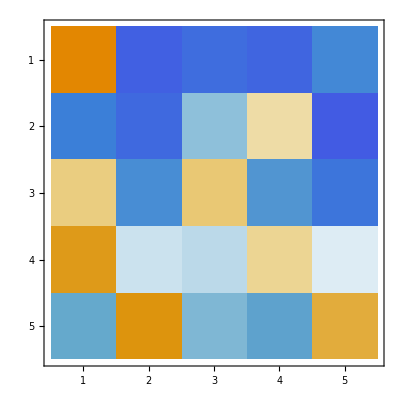
{-Graphics-,-Graphics-,-Graphics-}

{{5,2,3,1,4},2.4413×10^-16}

```mathematica
m=5;A=RandomReal[{-1,1},{m,m}];
{LU,p,c}=LUDecomposition[A];
L=LowerTriangularize[LU,-1]+IdentityMatrix[m];U =UpperTriangularize[LU];
Map[MatrixPlot,{A,A⟦p⟧,L.U}]
{p,Norm[A⟦p⟧-L.U]}
```

This pivot list is standard.  It is used to keep track of where the rows wind up.  At the end you get a list that would have put the matrix rows in a good order.

### Tracking Row Interchanges L and U Separate

At each step we scan what is left of column k for the largest element. We switch the rows to put the largest entry into the diagonal pivot spot and record the change by interchanging the matching entries in the pivot list.

Here is a modification of the non pivoted code.

```mathematica
Range[5]
```

{1,2,3,4,5}

```mathematica
Clear[PivotLUOne]
PivotLUOne[A_]:=Module[{m=Length[A],L,U=A,(* New *)p,col, i},
L=IdentityMatrix[m];
p=Range[m]; (* NEW *)
Do[
(* New *)
(* Find Max Position *)
col=Abs[U⟦All,k⟧]; col⟦1;;k-1⟧*=0;
i=FirstPosition[col,Max[col]]⟦1⟧;
(* Switch Rows Book Keeping *)
p⟦{k,i}⟧=p⟦{i,k}⟧;
(* Switch Rows *)
U⟦{k,i},k;;m⟧=U⟦{i,k},k;;m⟧;
L⟦{k,i},1;;k-1⟧=L⟦{i,k},1;;k-1⟧;
(* End New *)
Do[
L⟦j,k⟧=U⟦j,k⟧/U⟦k,k⟧;
U⟦j,k;;m⟧-=L⟦j,k⟧ U⟦k,k;;m⟧,
{j,k+1,m}],
{k,1,m-1}];
{L,U,(*New *)p}
]
```

As always test!

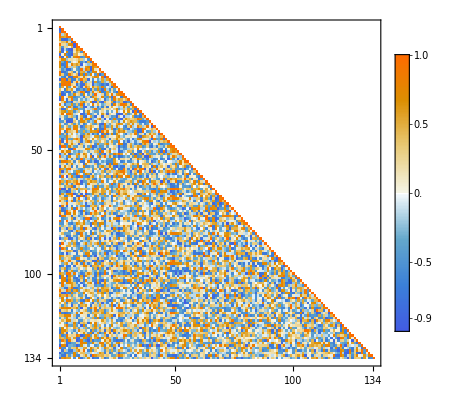
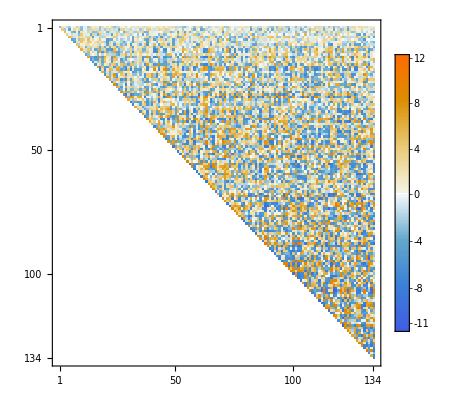

1.88153×10^-14

```mathematica
m=134;A=RandomReal[{-1,1},{m,m}];
{L,U,p}=PivotLUOne[A];
SetOptions[MatrixPlot, PlotLegends->Automatic];
Map[MatrixPlot,Chop[{L,U}]]
Norm[A⟦p⟧-L.U]
```

```mathematica
Sort[p];
```

This version stores L and U separately and actually copies rows of the matrices!  We are going to do another one that stores L and U together!

### Combining L and U

Here is a modification of the non pivoted code.  That combines L and U during the computation

```mathematica
Clear[LUTogether]
LUTogether[A_]:=Module[{m=Length[A],LU=A},
Do[
Do[
LU⟦j,k⟧=LU⟦j,k⟧/LU⟦k,k⟧;
(* Note the diagonals store the U not the L *)
(* Index range changed to exclude the diagonal *)
LU⟦j,k+1;;m⟧-=LU⟦j,k⟧ LU⟦k,k+1;;m⟧,
{j,k+1,m}],
{k,1,m-1}];
(* Splitting LU to maintain the return values *)
{LowerTriangularize[LU,-1]+IdentityMatrix[m],UpperTriangularize[LU]}
]
```

As always test!

```mathematica
m=134;A=RandomReal[{-1,1},{m,m}];
{L,U}=LUTogether[A];
Map[MatrixPlot,Chop[{L,U}]];
Norm[A-L.U]
```

1.60991×10^-12

### Pivoted LU Combined

This combines LU with pivoting.

```mathematica
Clear[LUTogetherPivoted]
LUTogetherPivoted[A_]:=Module[{m=Length[A],LU=A, p, col ,i},
p=Range[m]; 
Do[
(* Find Max Position *)
col=Abs[LU⟦All,k⟧]; col⟦1;;k-1⟧*=0;
i=FirstPosition[col,Max[col]]⟦1⟧;
(* Switch Rows Book Keeping *)
p⟦{k,i}⟧=p⟦{i,k}⟧;
(* Switch Rows *)
LU⟦{k,i}⟧=LU⟦{i,k}⟧;
Do[
LU⟦j,k⟧=LU⟦j,k⟧/LU⟦k,k⟧;
(* Diagonals store U not L. Index range excludes the diagonal. *)
LU⟦j,k+1;;m⟧-=LU⟦j,k⟧ LU⟦k,k+1;;m⟧,
{j,k+1,m}],
{k,1,m-1}];
(* Splitting LU to maintain the return values *)
{LowerTriangularize[LU,-1]+IdentityMatrix[m],UpperTriangularize[LU],p}
]
```

As always test!

```mathematica
m=123;A=RandomReal[{-1,1},{m,m}];
{L,U,p}=LUTogetherPivoted[A];
Norm[A⟦p⟧-L.U]
TabView[{
"L"->MatrixPlot[L,PlotLegends->Automatic],
"U"->MatrixPlot[U,PlotLegends->Automatic]}]
```

1.70674×10^-14

12

Pivoting has made sure |L_(i,j)|≤1 for all i and j. On the other hand the U values can (and do) get larger. A common measure of how bad a matrix is for partial pivoting is how big the U entries get!

## Sparse vs Dense

Dense matrices (the kind you are used to) are stored in a block of memory.  You should visualize it as a rectangular block of numbers. You describe which entry you are looking at by the row “i” and column “j” coordinates.

Non-zero entries of a sparse matrix are stored as a list of row “i” and column “j” coordinates along with the value z at that coordinate.  All other coordinates have the default value of 0.  The Mathematica format for this is 
	{
	{i_1,j_1}->z_1, 
	{i_2,j_2}->z_2,
	…
	{i_nz,j_nz}->z_1
	} 
where nz is simply the number of non-zero entries. It only makes sense to store a matrix that is almost all zeros as a sparse matrix.

It is easy to convert a sparse matrix to a dense matrix (assuming you have enough memory) in every software tool. If As is a sparse matrix then “Ad = Normal[As];” assigns the equivalent dense matrix to Ad. In Julia the equivalent command is “Ad = Matrix(As);”. In Matlab it is “Ad = full(As);”.

### Tiny Example

An examples building a sparse matrix should make this clear.

```mathematica
{m,n}={12,9};
nz=6;
AllCoords=Flatten[Table[{i,j},{i,m},{j,n}],1];
spCoords=RandomSample[AllCoords,nz];
spData=Table[
{i,j}=spCoords⟦k⟧;
{i,j}->RandomReal[{-1,1}],
{k,Length[spCoords]}];
As=SparseArray[spData,{m,n}];
Ad=Normal[As];
TabView[{
"Sparse"->As,
"Sparse Data"->spData,
"Dense Data"->Ad,
"Matrix" -> MatrixForm[As]
}]
```

1234

It is not a good idea to run an algorithm designed for a dense matrix on a sparse matrix! It might still work in either Mathematica or Julia but it will be very slow. In other languages it probably will just not work!

### Real Example

Here is a small sparse matrix from the NIST matrix market repository
	https://math.nist.gov/MatrixMarket/data/NEP/bfwave/bfw62a.html
I downloaded and uncompressed the standard Matrix Market interchange format (standard extension “.mtx”) file. The first 20 of the 452=450+2 lines are in the tab box below.  It is 88% zeros.

123

Fortunately we can just import things straight from the web! Our non-pivoted LUDecomposition works on both the sparse and dense versions of A and they produce identical dense output. The sparse one is just ten times slower than the other! This would only get worse for larger matrices.

```mathematica
A=Import["https://math.nist.gov/pub/MatrixMarket2/NEP/bfwave/bfw62a.mtx.gz"];
AbsoluteTiming[dLU=LUTogether[Normal[A]];]
AbsoluteTiming[sLU=LUTogether[A];]
```

{0.0768875,Null}

{0.607448,Null}

An LU decomposition of a sparse matrix is much less sparse!

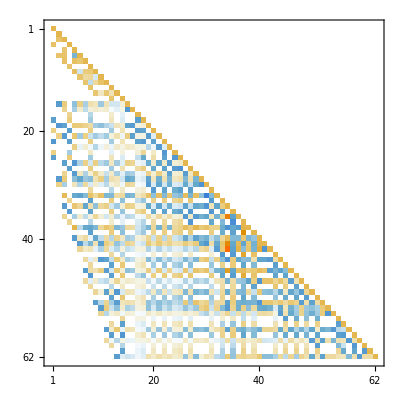
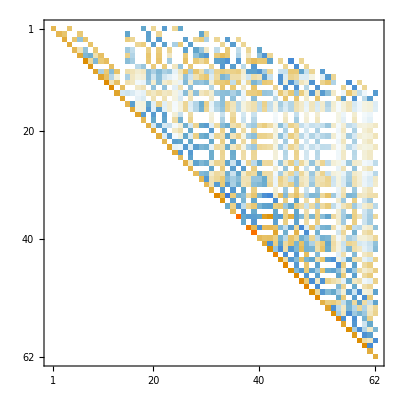

```mathematica
Map[MatrixPlot,sLU]
```

The output is now only 37% zeros.

```mathematica
1-Length[DeleteCases[Chop[Flatten[sLU⟦1⟧+sLU⟦2⟧]],0]]/62.0^2
```

0.374089

Just to repeat it is not a good idea to run an algorithm designed for a dense matrix on a sparse matrix! It might still work in either Mathematica or Julia but it will be significantly slower than converting the matrix to a dense format. In other languages it probably will just not work! It almost never makes sense to convert a dense matrix to sparse storage.

### Other Sparse Formats

The Wikipedia page
	https://en.wikipedia.org/wiki/Sparse_matrix
and the more technical Netlib documentation 
	http://www.netlib.org/utk/people/JackDongarra/etemplates/node372.html
discuss other storage formats the .mtx format (COO) on the wiki page was presumably chosen by NIST for their files since it is the simplest. In practice most sparse tools immediately convert sparse matrices to either Compressed Row Storage  (CRS on both web references)  or Compressed Column Storage (CCS on both web references).  CRS stores 
each row as a sparse vector. CCS stores each column as a sparse vector.

A sparse vector simply consists of a length n and two lists of n values: one contains the non-zero positions and the other the matching values. The cell below defines a length12 sparse vector in Mathematica

```mathematica
sv=SparseArray[{2->1.3,4->6.7, 9->-11.2},12];
TabView[{
"sv"->sv,
"dv"->Normal[sv]}]
```

12

Since lots of matrices are banded there are also “stripey” formats.